```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/joko/Git/MoneyModel/PKAssetPrices/plots/malware

```mathematica
ir=Import["import/ir_curves.csv"];
is=Import["import/is_ir_curves.csv"];
as=Import["import/as_curves.csv"];
ad=Import["import/ad_as_curves.csv"];
assets=Import["import/asset_market_curves.csv"];
bs=Import["import/balance_sheets.csv"];
```

```mathematica
{is[[All,2]],is[[All,1]]}
```

```mathematica
(*ticktrickX=Table[{k,k+2022},{k,{3,8,13,18,23,28,33}}]*)
ticktrickY1=Table[{k/100,ToString[k]<>"%"},{k,{6,8,10,12,14}}]
```

{{3/50,6%},{2/25,8%},{1/10,10%},{3/25,12%},{7/50,14%}}

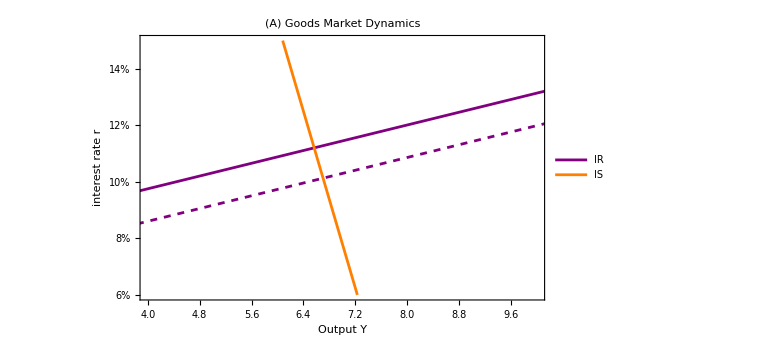

```mathematica
equ1=ListPlot[{ir[[All,{1,2}]],Transpose[{is[[All,2]],is[[All,1]]}],ir[[All,{1,3}]]},Joined->True,PlotStyle->{Purple, Orange, {Purple, Dashed}},Frame->True, PlotRange->{{4,10},{0.06,0.15}},FrameStyle->Black,FrameTicks->{{ticktrickY1,None},{Automatic, None}},
FrameLabel->{{Style["interest rate r",20],None},{Style["Output Y",20], None}},
PlotLegends->Placed[{Style["IR",20],Style["IS",20]},{Right,Bottom}],
PlotLabel->Style[Style["(A)",Bold]"Goods Market Dynamics",Black, 26],ImageSize->Large,FrameTicksStyle->Directive[{Black,20}],
GridLines->{Automatic, Automatic}]
```

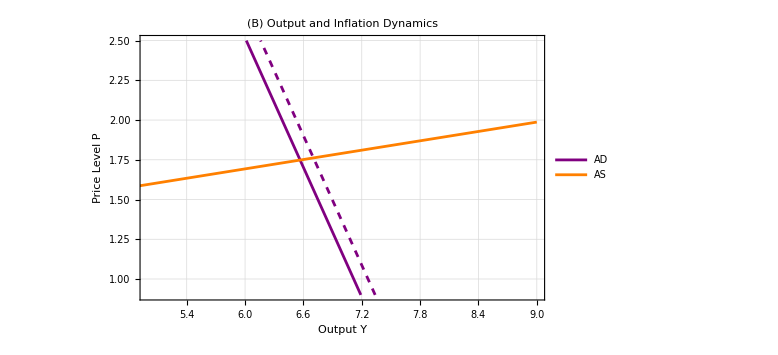

```mathematica
equ2=ListPlot[{ad[[All,{2,1}]],as[[All,{1,2}]],ad[[All,{3,1}]]},Joined->True,PlotStyle->{Purple, Orange, {Purple, Dashed}},Frame->True, PlotRange->{{5,9},{0.9,2.5}},FrameStyle->Black,FrameTicks->{{Automatic,None},{Automatic, None}},
FrameLabel->{{Style["Price Level P",20],None},{Style["Output Y",20], None}},
PlotLegends->Placed[{Style["AD",20],Style["AS",20]},{Right,Bottom}],
PlotLabel->Style[Style["(B)",Bold]"Output and Inflation Dynamics",Black, 26],ImageSize->Large,FrameTicksStyle->Directive[{Black,20}],
GridLines->{Automatic, Automatic}]
```

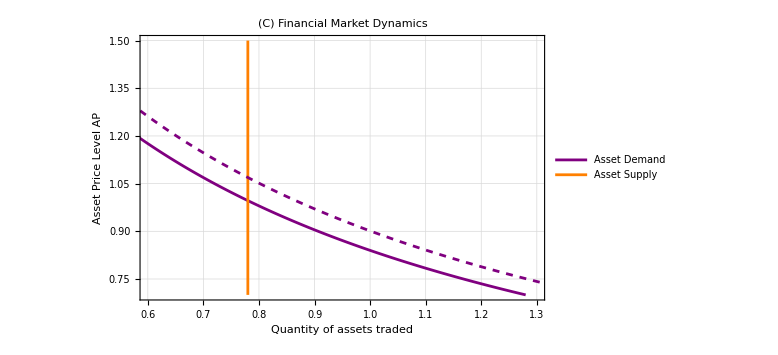

```mathematica
equ3=ListPlot[{assets[[All,{2,1}]],assets[[All,{4,1}]],assets[[All,{3,1}]]},Joined->True,PlotStyle->{Purple, Orange, {Purple, Dashed}},Frame->True, PlotRange->{{.6,1.3},{0.7,1.5}},FrameStyle->Black,FrameTicks->{{Automatic,None},{Automatic, None}},
FrameLabel->{{Style["Asset Price Level AP",20],None},{Style["Quantity of assets traded",20], None}},
PlotLegends->Placed[{Style["Asset Demand",20],Style["Asset Supply",20]},{Right,Top}],
PlotLabel->Style[Style["(C)",Bold]"Financial Market Dynamics",Black, 26],ImageSize->Large,FrameTicksStyle->Directive[{Black,20}],
GridLines->{Automatic, Automatic}]
```

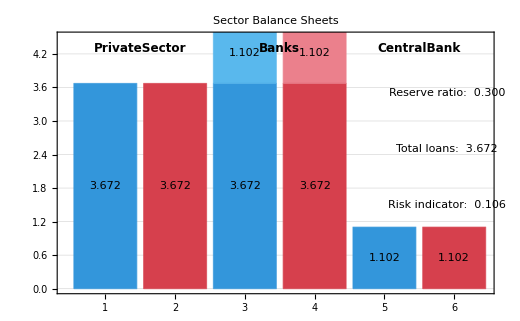

```mathematica
(*Balance sheet bar chart–replicates PDF panel*)(*data from equilibrium_values.csv*)dL=3.67167;dM=3.67167;dR=1.10150;SD=0.388658;

(*colours:blue for assets,red for liabilities*)
assetCol=RGBColor[0.20,0.59,0.86];
liabCol=RGBColor[0.84,0.25,0.30];
lightBlue=RGBColor[0.35,0.72,0.93];
lightRed=RGBColor[0.92,0.50,0.55];

(*6 stacked bars:Style[value,colour] per segment*)
bars={{Style[dM,assetCol]},(*PrivateSector·Assets*){Style[dL,liabCol]},(*PrivateSector·Liabilities*){Style[dL,assetCol],Style[dR,lightBlue]},(*Banks·Assets*){Style[dM,liabCol],Style[dR,lightRed]},(*Banks·Liabilities*){Style[dR,assetCol]},(*CentralBank·Assets*){Style[dR,liabCol]}                                    (*CentralBank·Liabilities*)};

labels={"Assets\nPrivate\nSector","Liabilities\nPrivate\nSector","Assets\nBanks","Liabilities\nBanks","Assets\nCentral\nBank","Liabilities\nCentral\nBank"};

(*── bar chart ──*)
chart=BarChart[bars,ChartLayout->"Stacked",BarOrigin->Bottom,ChartLabels->Placed[labels,Axis,Rotate[#,Pi/4,{0,1}]&],LabelingFunction->(Placed[NumberForm[#,{4,3}],Center]&),Axes->{False,True},Frame->{{Left,False},{Bottom,True}},FrameLabel->{{None,None},{None,Style["Amount",12]}},GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Dashed,Opacity[0.2]],PlotRange->{All,{0,4.5}},ImageSize->520,AspectRatio->1/GoldenRatio,PlotLabel->Style["Sector Balance Sheets",Bold,14],ImageSize->Large];

(*── annotations (sector names+indicators) ──*)
annotations=Graphics[{Text[Style["PrivateSector",Bold,12],{1.5,4.3}],Text[Style["Banks",Bold,12],{3.5,4.3}],Text[Style["CentralBank",Bold,12],{5.5,4.3}],Text[Style["Reserve ratio:  "<>ToString[NumberForm[dR/dM,{4,3}]],Medium],{5.9,3.5},{1,0}],Text[Style["Total loans:  "<>ToString[NumberForm[dL,{4,3}]],Medium],{5.9,2.5},{1,0}],Text[Style["Risk indicator:  "<>ToString[NumberForm[SD/dL,{4,3}]],Medium],{5.9,1.5},{1,0}]}];

equ4=Show[chart,annotations]
```

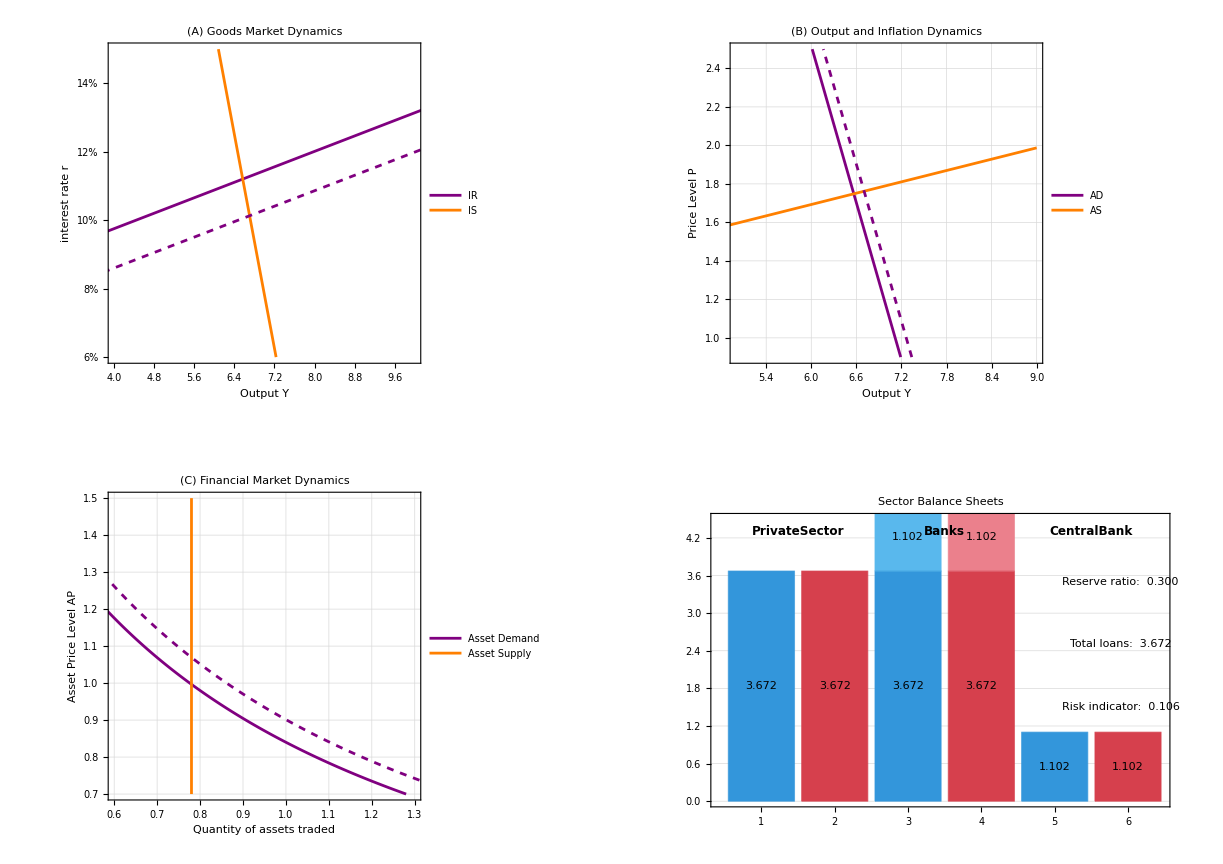

```mathematica
GraphicsGrid[{{equ1,equ2},{equ3,equ4}},Spacings->{20,20},ImageSize->Large]
```